```mathematica
Thread[Join[{{{1},{2,3},{3,4,5}},{{2,3,4},{3,2},{019}}}]]
```

{{{1},{2,3,4}},{{2,3},{3,2}},{{3,4,5},{19}}}

```mathematica
Join[{1},{2,3,4}]
```

{1,2,3,4}

```mathematica
Thread[Join[{{a,b,c},{x,y,z}}]]
```

{{a,x},{b,y},{c,z}}

```mathematica
Join[{1},{2,3,4}]
```

{1,2,3,4}

```mathematica
Flatten[{{1},{2,3,4}}]
```

{1,2,3,4}

```mathematica
Flatten/@Thread[Join[{{{1},{2,3},{3,4,5}},{{2,3,4},{3,2},{019}}}]]
```

{{1,2,3,4},{2,3,3,2},{3,4,5,19}}

```mathematica
Thread[Join[{{1,2},{3,4}}]]
```

{{1,3},{2,4}}

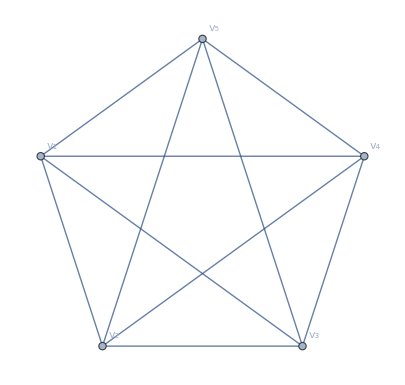

```mathematica
g=CompleteGraph[5,VertexLabels->Table[i->Subscript[v, i],{i,5}]]
```

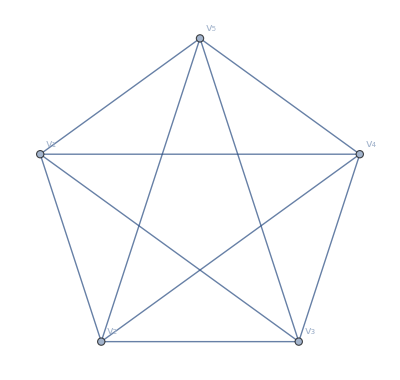
FindGraphIsomorphism[-Graphics-,Graph[{v_4,x},{v_4,y},{v_4,z},{v_4,x,y,z}]]

```mathematica
FindGraphIsomorphism[g,Graph[{Subscript[v, 4],x},{Subscript[v, 4],y},{Subscript[v, 4],z},{Subscript[v, 4],x,y,z}]]
```

```mathematica
FullForm[g]
```

Graph[List[1,2,3,4,5],List[Null,SparseArray[Automatic,List[5,5],0,List[1,List[List[0,4,8,12,16,20],List[List[2],List[3],List[4],List[5],List[1],List[3],List[4],List[5],List[1],List[2],List[4],List[5],List[1],List[2],List[3],List[5],List[1],List[2],List[3],List[4]]],Pattern]]],List[Rule[GraphLayout,"CircularEmbedding"],Rule[VertexLabels,List[Rule[3,Subscript[v,3]],Rule[5,Subscript[v,5]],Rule[4,Subscript[v,4]],Rule[2,Subscript[v,2]],Rule[1,Subscript[v,1]]]]]]

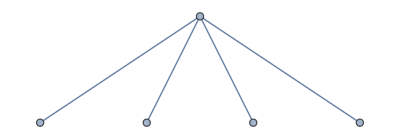

```mathematica
g2=Graph[{{1,2},{1,3},{1,4},{1,5}}]
```

```mathematica
FullForm[%]
```

Graph[List[1,2,3,4],List[UndirectedEdge[1,2],UndirectedEdge[1,3],UndirectedEdge[1,4]]]

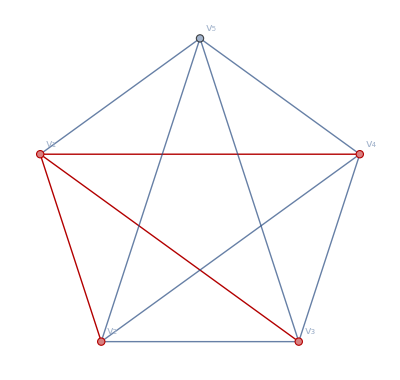

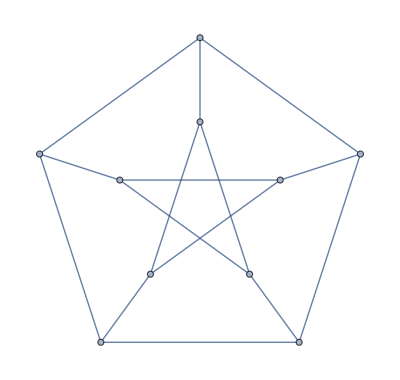
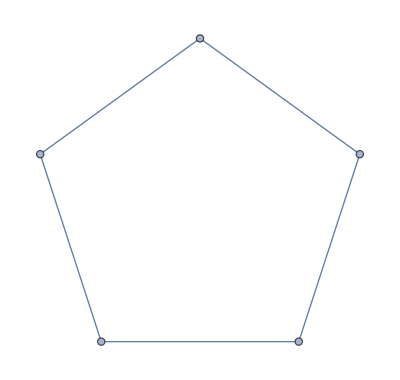

```mathematica
HighlightGraph[g,g2,GraphHighlightStyle->"Thick"]
```

```mathematica
s=Subsets[Range[VertexCount[g]],{VertexCount[g2]}];
```

```mathematica
Select[Subgraph[g,#]&/@s,IsomorphicGraphQ[#,g2]&];
```

```mathematica
HighlightGraph[g,#]&/@%
```

{}

```mathematica
g
```



```mathematica
g2
```


{-Graphics-,-Graphics-}

```mathematica
{g,h}={CompleteGraph[5],g2}
```

```mathematica
s=Subsets[Range[VertexCount[g]],{VertexCount[h]}];
```

```mathematica
Select[Subgraph[g,#]&/@s,IsomorphicGraphQ[#,h]&];
```

```mathematica
HighlightGraph[g,#]&/@%
```

{}